```mathematica
nf=50;
μ=20;
```

If you are using this notebook, I have already generated the results of the discrete model for nf = 50 above.
You can just go to the second section and import the definitions and not have to rerun the differential equation solver.

## Generating/Solving the Differential Equations (takes a while)

Factor of 1/2 here comes from the fact that we are not counting atoms in this model but the probability for the sample to be in an "atom state"

```mathematica
ClearAll[n,P]
eqns=Table[P[i]'[t]==0.5(If[i≠ 0,-β i(i-1)P[i][t],0]+β (i+2)(i+1)P[i+2][t]),{i,0,nf-2}]
P[nf][t]=P0[nf]Exp[-0.5β nf(nf-1)t];
P[nf-1][t]=P0[nf-1]Exp[-0.5β(nf-1)(nf-2)t];
```

{P[0]'[t]==1. β P[2][t],P[1]'[t]==3. β P[3][t],P[2]'[t]==0.5 (-2 β P[2][t]+12 β P[4][t]),P[3]'[t]==0.5 (-6 β P[3][t]+20 β P[5][t]),P[4]'[t]==0.5 (-12 β P[4][t]+30 β P[6][t]),P[5]'[t]==0.5 (-20 β P[5][t]+42 β P[7][t]),P[6]'[t]==0.5 (-30 β P[6][t]+56 β P[8][t]),P[7]'[t]==0.5 (-42 β P[7][t]+72 β P[9][t]),P[8]'[t]==0.5 (-56 β P[8][t]+90 β P[10][t]),P[9]'[t]==0.5 (-72 β P[9][t]+110 β P[11][t]),P[10]'[t]==0.5 (-90 β P[10][t]+132 β P[12][t]),P[11]'[t]==0.5 (-110 β P[11][t]+156 β P[13][t]),P[12]'[t]==0.5 (-132 β P[12][t]+182 β P[14][t]),P[13]'[t]==0.5 (-156 β P[13][t]+210 β P[15][t]),P[14]'[t]==0.5 (-182 β P[14][t]+240 β P[16][t]),P[15]'[t]==0.5 (-210 β P[15][t]+272 β P[17][t]),P[16]'[t]==0.5 (-240 β P[16][t]+306 β P[18][t]),P[17]'[t]==0.5 (-272 β P[17][t]+342 β P[19][t]),P[18]'[t]==0.5 (-306 β P[18][t]+380 β P[20][t]),P[19]'[t]==0.5 (-342 β P[19][t]+420 β P[21][t]),P[20]'[t]==0.5 (-380 β P[20][t]+462 β P[22][t]),P[21]'[t]==0.5 (-420 β P[21][t]+506 β P[23][t]),P[22]'[t]==0.5 (-462 β P[22][t]+552 β P[24][t]),P[23]'[t]==0.5 (-506 β P[23][t]+600 β P[25][t]),P[24]'[t]==0.5 (-552 β P[24][t]+650 β P[26][t]),P[25]'[t]==0.5 (-600 β P[25][t]+702 β P[27][t]),P[26]'[t]==0.5 (-650 β P[26][t]+756 β P[28][t]),P[27]'[t]==0.5 (-702 β P[27][t]+812 β P[29][t]),P[28]'[t]==0.5 (-756 β P[28][t]+870 β P[30][t]),P[29]'[t]==0.5 (-812 β P[29][t]+930 β P[31][t]),P[30]'[t]==0.5 (-870 β P[30][t]+992 β P[32][t]),P[31]'[t]==0.5 (-930 β P[31][t]+1056 β P[33][t]),P[32]'[t]==0.5 (-992 β P[32][t]+1122 β P[34][t]),P[33]'[t]==0.5 (-1056 β P[33][t]+1190 β P[35][t]),P[34]'[t]==0.5 (-1122 β P[34][t]+1260 β P[36][t]),P[35]'[t]==0.5 (-1190 β P[35][t]+1332 β P[37][t]),P[36]'[t]==0.5 (-1260 β P[36][t]+1406 β P[38][t]),P[37]'[t]==0.5 (-1332 β P[37][t]+1482 β P[39][t]),P[38]'[t]==0.5 (-1406 β P[38][t]+1560 β P[40][t]),P[39]'[t]==0.5 (-1482 β P[39][t]+1640 β P[41][t]),P[40]'[t]==0.5 (-1560 β P[40][t]+1722 β P[42][t]),P[41]'[t]==0.5 (-1640 β P[41][t]+1806 β P[43][t]),P[42]'[t]==0.5 (-1722 β P[42][t]+1892 β P[44][t]),P[43]'[t]==0.5 (-1806 β P[43][t]+1980 β P[45][t]),P[44]'[t]==0.5 (-1892 β P[44][t]+2070 β P[46][t]),P[45]'[t]==0.5 (-1980 β P[45][t]+2162 β P[47][t]),P[46]'[t]==0.5 (-2070 β P[46][t]+2256 β P[48][t]),P[47]'[t]==0.5 (-2162 β P[47][t]+2352 β P[49][t]),P[48]'[t]==0.5 (-2256 β P[48][t]+2450 β P[50][t])}

```mathematica
Timing[For[k=nf-2,k>=0,k=k-1,
Print[k];
P[k][t]=P[k][t]/.DSolve[{P[k]'[t]==0.5(If[k≠ 0,-β k(k-1)P[k][t],0]+β (k+2)(k+1)P[k+2][t]),P[k][0]==P0[k]},P[k][t],t][[1]]
]]
```

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

{972.078125,Null}

```mathematica
SetDirectory[NotebookDirectory[]]
Definition[P]>>"nbar_2.m"
```

D:\users\ebert\Dropbox\Mathematica\TwoBodyLoss

```mathematica
subs=Append[Table[P0[k]->N@PDF[PoissonDistribution[10],k],{k,0,nf}],t->tb/β];
```

```mathematica
Clear[nbar]
```

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
nbar[mean_,tb_]:=Evaluate@ParallelSum[k P[k][t]/.subs,{k,0,nf}]
```

```mathematica
nbar[10,1]
```

1.09221

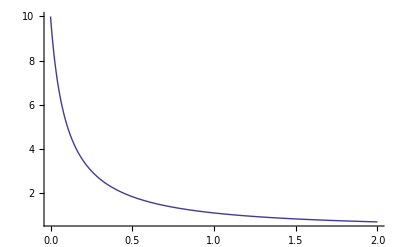

```mathematica
Plot[Evaluate[nbar[10,tb]/.tb->t],{t,0,2},PlotRange->All]
```

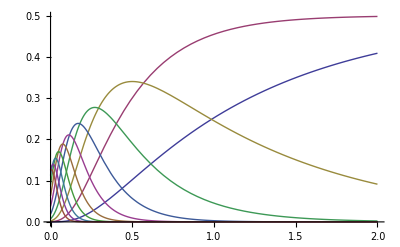

```mathematica
Plot[Evaluate@Table[Evaluate[(P[k][t]/.subs)]/.tb->t,{k,0,10}],{t,0,2},PlotRange->All]
```

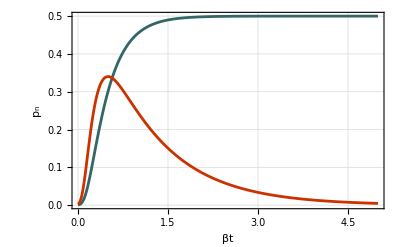

```mathematica
Plot[Evaluate@Table[Evaluate[(P[k][t]/.subs)]/.tb->t,{k,1,2}],{t,0,5},Frame->True,FrameLabel->Evaluate[Style[#,20]&/@{"βt","p_n"}],GridLines->Automatic,GridLinesStyle->GrayLevel[0.8],PlotStyle->(Directive[AbsoluteThickness[2],PointSize[Medium],#]&/@ColorData[64,"ColorList"])[[{1,3}]],PlotRange->All]
```

```mathematica
Qparam[data__]:=Module[{mean,nsq},
mean=Total[data Range[0,Length[data]-1]];
nsq=Total[data(Range[0,Length[data]-1]^2)];
Return[(nsq-mean^2)/mean-1];
]
```

```mathematica
qdata=Table[{tp,Qparam[Table[Evaluate[P[k][t]/.subs]/.tb->tp,{k,0,20}]]},{tp,0,5,.05}];
```

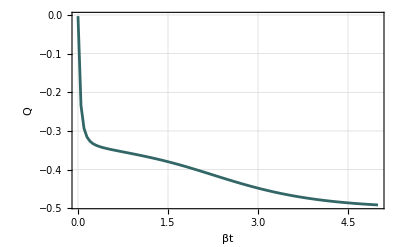

```mathematica
ListLinePlot[qdata,Frame->True,FrameLabel->Evaluate[Style[#,20]&/@{"βt","Q"}],GridLines->Automatic,GridLinesStyle->GrayLevel[0.8],PlotRange->All,PlotStyle->(Directive[AbsoluteThickness[2],PointSize[Medium],#]&/@ColorData[64,"ColorList"])[[1]]]
```

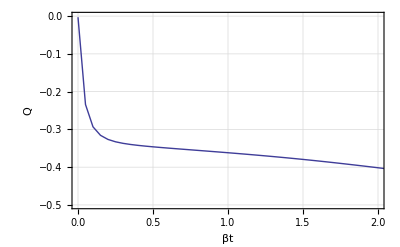

```mathematica
ListLinePlot[qdata,Frame->True,FrameLabel->{"βt","Q"},GridLines->Automatic,GridLinesStyle->GrayLevel[0.8],PlotRange->{{0,2},{-0.5,0}}]
```

```mathematica
(nsq-mean)/nsq-1
```

-0.40268834344881

```mathematica
Maximize[{Evaluate[P[2][t]/.subs],t>10,t<100},t]
```

{0.340102,{t→50.0469}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\users\ebert\Dropbox\Mathematica\TwoBodyLoss

```mathematica
Definition[nbar]>>>"nbar_2.m"
```

```mathematica
int=Integrate[nbar[mean,beta,t],{t,0,tex}];
```

```mathematica
MAReadoutModel[mean_,beta_,gamma_,tex_]:= Evaluate@(gamma int)
```

```mathematica
ClearAll[t,tex]
```

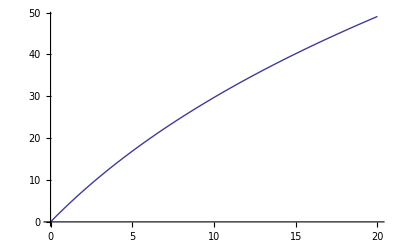

```mathematica
Plot[MAReadoutModel[4,0.02,1,t],{t,0,20}]
```

```mathematica
Definition[MAReadoutModel]>>>"nbar_2.m"
```

```mathematica
ndecay[nstart_Integer,beta_,t_]:=Evaluate[Sum[k P[k][t]/.Append[Table[P0[k]->KroneckerDelta[k,nstart],{k,1,nf}],β->beta],{k,1,nf}]]
```

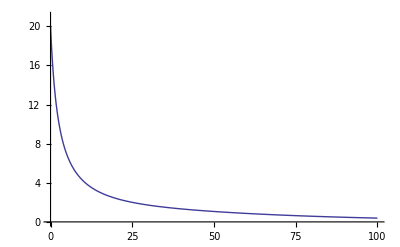

```mathematica
Plot[Evaluate@ndecay[20,0.02,t],{t,0,100},PlotRange->{0,21}]
```

```mathematica
ndecay[2,1,t]/.t->1.
```

0.735759

```mathematica
Definition[ndecay]>>>"nbar_2.m"
```

## Using Solutions

### Read in the definitions from the file

```mathematica
SetDirectory@NotebookDirectory[]
```

E:\Dropbox\thesis\mameasurements

```mathematica
<<"nbar_2.m"
```

```mathematica
IntCamSigModel[Γ_,β_,n_,x_]:=Γ Log[1+(-1+E^(x β)) n]/β
```

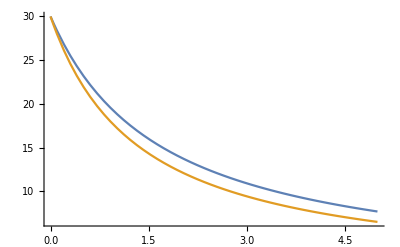

```mathematica
Plot[{ndecay[30,0.02,t],ndecay[30,0.025,t]},{t,0,5},PlotRange->{0,All}]
```

```mathematica
(* Produce list of signals from n=1 to nf after exposure for tex time*)
centers[beta_,tex_]:=Evaluate@(Integrate[ndecay[#,beta,t],{t,0,tex}]&/@Range[nf])
```

```mathematica
Sum[PDF[PoissonDistribution[#],k] ,{k,nf}]&/@Range[10,50,10]//N
```

{0.999955,1.,0.999702,0.947372,0.537517}

```mathematica
nf
```

50

```mathematica
ndecay[3,0.02,1]
```

2.88353

```mathematica
data={};
For[nb=5,nb≤20,nb+=5,
weights=Table[PDF[PoissonDistribution[nb],k] ,{k,nf}];
AppendTo[data,Table[{t,Total[weights centers[0.02,t]]},{t,0,20,0.1}]];
]
```

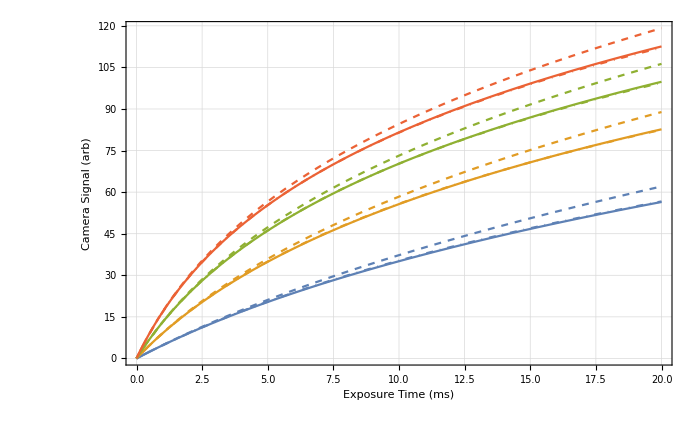

```mathematica
comp=Show[
Plot[Evaluate@Table[IntCamSigModel[1,0.02,n,tex],{n,Range[5,20,5]}],{tex,0,20},PlotStyle->{Dashed},Frame->True,FrameLabel->{"Exposure Time (ms)","Camera Signal (arb)"},LabelStyle->Directive[Bold, Large],GridLines->Automatic,GridLinesStyle->LightGray],
ListLinePlot[data],
Plot[Evaluate@Table[Log[(a+(-1+ⅇ^(a b tp)) n0)/a]/b/.{b->0.02,a->0.25259530475410125,tp->tex,n0->n},{n,Range[5,20,5]}],{tex,0,20},PlotStyle->{DotDashed}],
ImageSize->700
]
```

```mathematica
fit=NonlinearModelFit[data[[2]],Log[(a+(-1+ⅇ^(a b tp)) n0)/a]/b/.{b->0.02,n0->10},{{a,0.5}},tp]
```

FittedModel[50. Log[3.9589 (0.252595+10 (-1+ⅇ^(0.00505191 tp)))]]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.252595 | 0.00135361 | 186.609 | 2.63021×10^-226

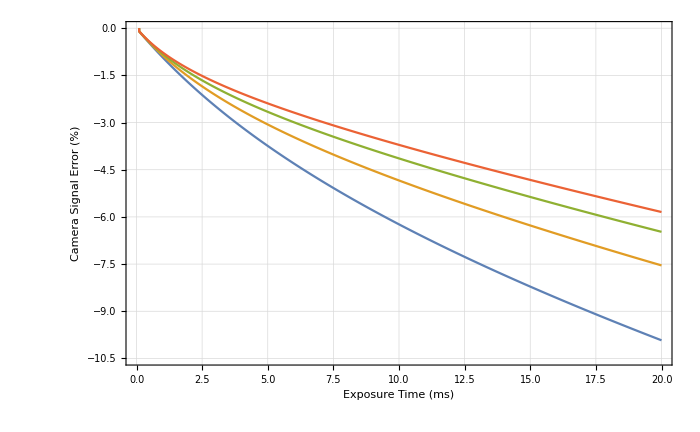

```mathematica
texs=Range[0,20,0.1];
error=ListLinePlot[Evaluate@Table[{texs[[texi]],100*(data[[i,texi,2]]-IntCamSigModel[1,0.02,Range[5,20,5][[i]],texs[[texi]]])/data[[i,texi,2]]},{i,4},{texi,Range@Length@texs}],Frame->True,FrameLabel->{"Exposure Time (ms)","Camera Signal Error (%)"},LabelStyle->Directive[Bold, Large],GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->700,PlotRange->{-10.5,0}]
```

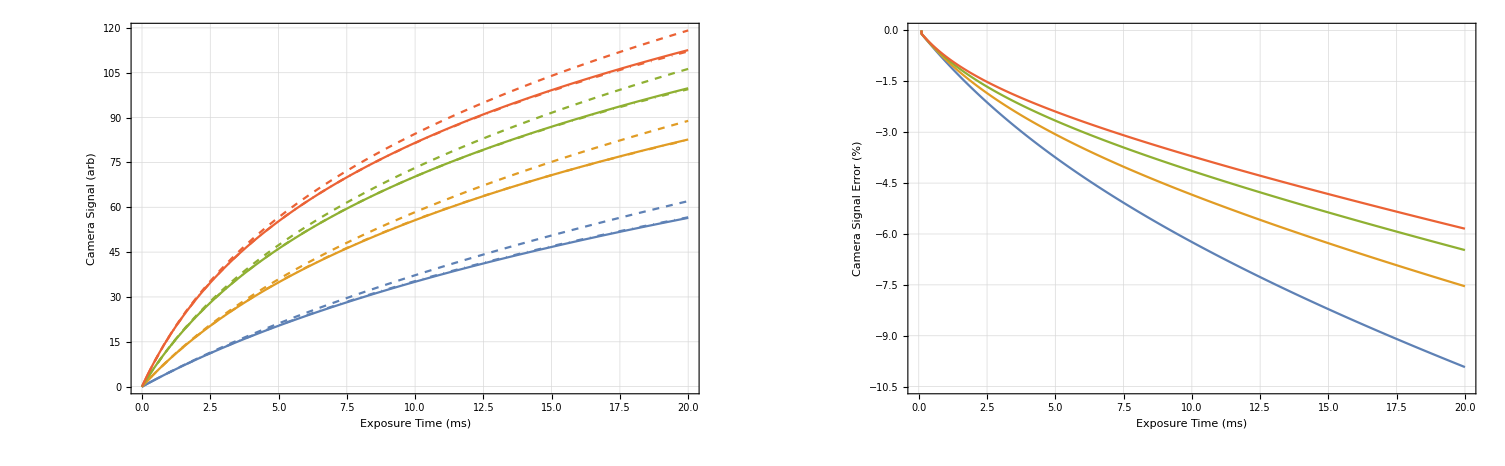

```mathematica
comprow=GraphicsRow[{comp,error}]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

E:\Dropbox\thesis\mameasurements

```mathematica
Export["masim.pdf",comprow]
Export["masim.eps",comprow]
Export["masim.png",comprow]
```

masim.pdf

masim.eps

masim.png

## More Comparisons

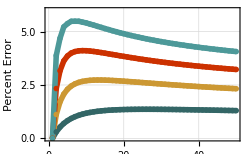

```mathematica
markers = {{-Graphics-, 0.02}, {-Graphics-, 0.02}, {-Graphics-, 0.02}, {-Graphics-, 0.02}};
percenterror=ListLinePlot[100(Table[IntCamSigModel[1,0.02,n,tex],{tex,{5,10,15,20}},{n,1,nf}]-Table[centers[0.02,tex],{tex,{5,10,15,20}}])/Table[centers[0.02,tex],{tex,{5,10,15,20}}],FrameLabel->{"","Percent Error"},
Frame->True,
ImageSize->250,
LabelStyle->Medium,
PlotRange->{0,6},
GridLines->Automatic,
GridLinesStyle->GrayLevel[0.9],
PlotStyle->(Directive[AbsoluteThickness[4],PointSize[Medium],#]&/@ColorData[64,"ColorList"]),
PlotMarkers->Transpose[{markers [[All,1]],2markers [[All,2]]}]
]
```

```mathematica
Clear[PlotLegends]
```

Clear::wrsym: Symbol PlotLegends is Protected.

```mathematica
Remove["PlotLegends`*"]
```

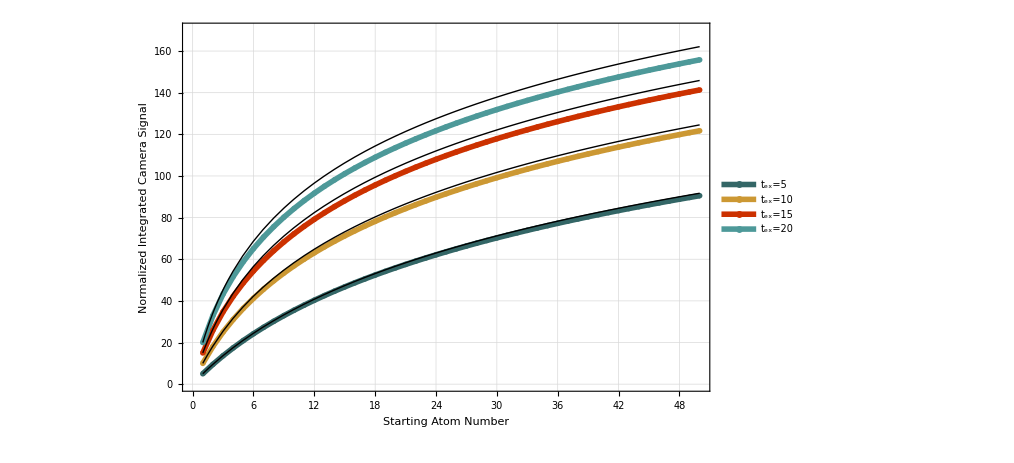

```mathematica
masim=Show[
ListLinePlot[Table[centers[0.02,tex],{tex,{5,10,15,20}}],FrameLabel->{"Starting Atom Number","Normalized Integrated Camera Signal"},Frame->True,LabelStyle->Directive[Large],
ImageSize->750,
PlotStyle->(Directive[AbsoluteThickness[4],PointSize[Medium],#]&/@ColorData[64,"ColorList"]),
PlotRange->{0,170},
GridLines->Automatic,
GridLinesStyle->GrayLevel[0.9],
Epilog->Inset[percenterror,{40,30}],
PlotMarkers->markers ,
PlotLegends->Placed[LineLegend[Row[{"t_ex=",#1}]&/@Range[5,20,5],
LegendMarkers->markers,
LegendMarkerSize->{25,12},
LabelStyle->{GrayLevel[0.3],Bold,16}
],{0.1,0.73}]
],
Plot[Table[IntCamSigModel[1,0.02,n,tex],{tex,{5,10,15,20}}],{n,1,nf},PlotStyle->{Black,Thick}]
]
```

```mathematica
Definition[PlotLegends]
```

Attributes[PlotLegends]={Protected,ReadProtected}

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\users\ebert\Mathematica\ShortExposureTime

## Histograms

```mathematica
centers2[beta_,tex_]:=Evaluate@centers[beta,tex]
HistCamSigModel2[s0_,s_,β_,camEx_,n0_,x_]:=Evaluate@(PDF[PoissonDistribution[n0],0]/(s0 Sqrt[2π]) Exp[-(x)^2/(2 s0^2)]+Sum[PDF[PoissonDistribution[n0],k]/(s Sqrt[k] Sqrt[2π]) Exp[-(x-centers2[β,camEx][[k]]/camEx)^2/(2s^2 k)],{k,1,nf}]);
```

```mathematica
Definition[HistCamSigModel]
```

HistCamSigModel[QCFunctions`Private`s0_,QCFunctions`Private`s_,QCFunctions`Private`β_,QCFunctions`Private`camEx_,QCFunctions`Private`n0_,QCFunctions`Private`x_]:=(QCFunctions`Private`PMF[QCFunctions`Private`n0,0] Exp[-(QCFunctions`Private`x)^2/(2 (QCFunctions`Private`s0)^2)])/(QCFunctions`Private`s0 √(2 π))+∑_(QCFunctions`Private`k=1)^50 (QCFunctions`Private`PMF[QCFunctions`Private`n0,QCFunctions`Private`k] Exp[-(QCFunctions`Private`x-QCFunctions`Private`centers[QCFunctions`Private`k,QCFunctions`Private`β,QCFunctions`Private`camEx])^2/(2 (QCFunctions`Private`s)^2 QCFunctions`Private`k)])/(QCFunctions`Private`s √(QCFunctions`Private`k) √(2 π))

```mathematica
Definition[HistCamSigModel2]>>>"nbar.m"
```

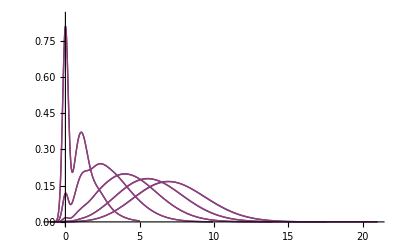

```mathematica
Show[Table[Plot[{HistCamSigModel2[0.188,0.448,0.02,3,k,x],HistCamSigModel[0.188,0.448,0.02,3,k,x]},{x,-1,k+4 √k},PlotRange->{0,.85}],
{k,9,1,-2}]]
```

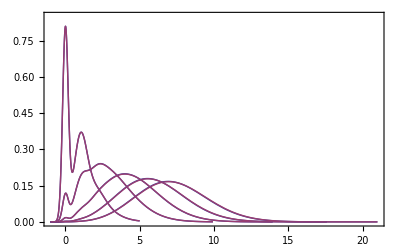

```mathematica
Show[%82,Frame->True]
```

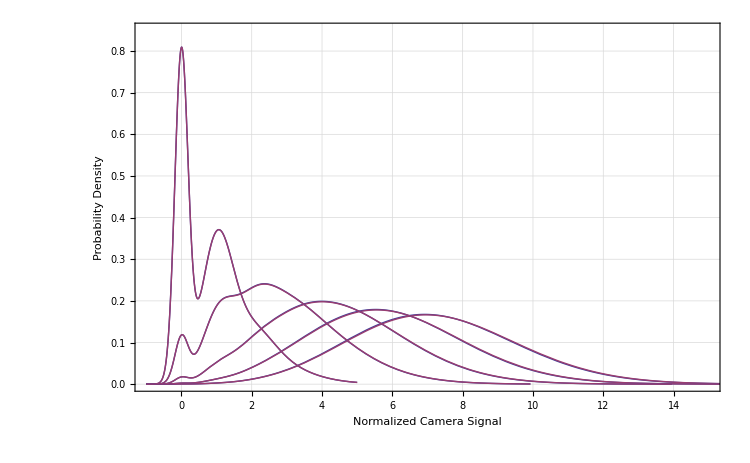

```mathematica
Show[%,LabelStyle->Directive[Large],ImageSize->750]
```

```mathematica
HistCamSigModel2[0.188,0.448,0.02,3,10,x]
```

2.12203 ⅇ^(-10-14.1467 x^2)+8.90496 ⅇ^(-10-2.49123 (x-centers2[1,0.02,3])^2)+31.4838 ⅇ^(-10-1.24562 (x-centers2[2,0.02,3])^2)+85.688 ⅇ^(-10-0.83041 (x-centers2[3,0.02,3])^2)+185.52 ⅇ^(-10-0.622808 (x-centers2[4,0.02,3])^2)+331.868 ⅇ^(-10-0.498246 (x-centers2[5,0.02,3])^2)+504.922 ⅇ^(-10-0.415205 (x-centers2[6,0.02,3])^2)+667.809 ⅇ^(-10-0.35589 (x-centers2[7,0.02,3])^2)+780.848 ⅇ^(-10-0.311404 (x-centers2[8,0.02,3])^2)+817.99 ⅇ^(-10-0.276803 (x-centers2[9,0.02,3])^2)+776.013 ⅇ^(-10-0.249123 (x-centers2[10,0.02,3])^2)+672.636 ⅇ^(-10-0.226476 (x-centers2[11,0.02,3])^2)+536.666 ⅇ^(-10-0.207603 (x-centers2[12,0.02,3])^2)+396.625 ⅇ^(-10-0.191633 (x-centers2[13,0.02,3])^2)+272.998 ⅇ^(-10-0.177945 (x-centers2[14,0.02,3])^2)+175.828 ⅇ^(-10-0.166082 (x-centers2[15,0.02,3])^2)+106.403 ⅇ^(-10-0.155702 (x-centers2[16,0.02,3])^2)+60.721 ⅇ^(-10-0.146543 (x-centers2[17,0.02,3])^2)+32.7835 ⅇ^(-10-0.138402 (x-centers2[18,0.02,3])^2)+16.7943 ⅇ^(-10-0.131117 (x-centers2[19,0.02,3])^2)+8.18451 ⅇ^(-10-0.124562 (x-centers2[20,0.02,3])^2)+3.80346 ⅇ^(-10-0.11863 (x-centers2[21,0.02,3])^2)+1.6891 ⅇ^(-10-0.113238 (x-centers2[22,0.02,3])^2)+0.718247 ⅇ^(-10-0.108314 (x-centers2[23,0.02,3])^2)+0.292968 ⅇ^(-10-0.103801 (x-centers2[24,0.02,3])^2)+0.11482 ⅇ^(-10-0.0996492 (x-centers2[25,0.02,3])^2)+0.0433038 ⅇ^(-10-0.0958166 (x-centers2[26,0.02,3])^2)+0.0157386 ⅇ^(-10-0.0922678 (x-centers2[27,0.02,3])^2)+0.00551966 ⅇ^(-10-0.0889725 (x-centers2[28,0.02,3])^2)+0.00187023 ⅇ^(-10-0.0859045 (x-centers2[29,0.02,3])^2)+0.000612931 ⅇ^(-10-0.083041 (x-centers2[30,0.02,3])^2)+0.000194504 ⅇ^(-10-0.0803623 (x-centers2[31,0.02,3])^2)+0.0000598254 ⅇ^(-10-0.077851 (x-centers2[32,0.02,3])^2)+0.0000178521 ⅇ^(-10-0.0754918 (x-centers2[33,0.02,3])^2)+5.17283×10^-6 ⅇ^(-10-0.0732715 (x-centers2[34,0.02,3])^2)+1.45668×10^-6 ⅇ^(-10-0.071178 (x-centers2[35,0.02,3])^2)+3.98975×10^-7 ⅇ^(-10-0.0692009 (x-centers2[36,0.02,3])^2)+1.06364×10^-7 ⅇ^(-10-0.0673306 (x-centers2[37,0.02,3])^2)+2.76198×10^-8 ⅇ^(-10-0.0655587 (x-centers2[38,0.02,3])^2)+6.9906×10^-9 ⅇ^(-10-0.0638777 (x-centers2[39,0.02,3])^2)+1.72567×10^-9 ⅇ^(-10-0.0622808 (x-centers2[40,0.02,3])^2)+4.1573×10^-10 ⅇ^(-10-0.0607617 (x-centers2[41,0.02,3])^2)+9.77978×10^-11 ⅇ^(-10-0.059315 (x-centers2[42,0.02,3])^2)+2.24777×10^-11 ⅇ^(-10-0.0579356 (x-centers2[43,0.02,3])^2)+5.05017×10^-12 ⅇ^(-10-0.0566189 (x-centers2[44,0.02,3])^2)+1.10972×10^-12 ⅇ^(-10-0.0553607 (x-centers2[45,0.02,3])^2)+2.38607×10^-13 ⅇ^(-10-0.0541572 (x-centers2[46,0.02,3])^2)+5.02245×10^-14 ⅇ^(-10-0.0530049 (x-centers2[47,0.02,3])^2)+1.03539×10^-14 ⅇ^(-10-0.0519006 (x-centers2[48,0.02,3])^2)+2.09136×10^-15 ⅇ^(-10-0.0508414 (x-centers2[49,0.02,3])^2)+4.14068×10^-16 ⅇ^(-10-0.0498246 (x-centers2[50,0.02,3])^2)